## Twisted bilayer WSe_2 theory

In these notes we will calculate the ARPES response for the flat bands generated around Γ in twisted bilayer WSe_2.

### Basic WSe2/WS2 parameters

```mathematica
(* Lattice constants (in nm). These numbers are based on ... *)
aWSe2=0.332;
aWS2=0.318;
(* Lattice vectors: for the big BZ *)
a1Se=aWSe2*{1,0};
a2Se=aWSe2*1/2*{1,Sqrt[3]};
a1S=aWSe2*{1,0};
a2S=aWSe2*1/2*{1,Sqrt[3]};
(* Nearest neighbor W in a monolayer *)
δ1Se=aWSe2*{0,1/Sqrt[3]};
δ2Se=aWSe2*{-1/2,-1/(2 √3)};
δ3Se=aWSe2*{1/2,-1/(2 √3)};
δ1S=aWS2*{0,1/Sqrt[3]};
δ2S=aWS2*{-1/2,-1/(2 √3)};
δ3S=aWS2*{1/2,-1/(2 √3)};
(* Momentum structure of interlayer hopping *)
γSe[k_]:=(Exp[I*k.δ1Se]+Exp[I*k.δ2Se]+Exp[I*k.δ3Se])/3;
γS[k_]:=(Exp[I*k.δ1S]+Exp[I*k.δ2S]+Exp[I*k.δ3S])/3;
(* Reciprocal lattice vectors (big BZ) *)
{G1,G2}=2*Pi*Inverse[Transpose[{a1Se,a2Se}]];
G3={-1,1}*G1;
KbigBZ=(2*G1+G2)/3;
MbigBZ=G1/2;
ΓMlength=2*Pi/Sqrt[3]/aWSe2;
{G1,G2}=2*Pi*Inverse[Transpose[{a1S,a2S}]];
G3={-1,1}*G1;
KbigBZ=(2*G1+G2)/3;
MbigBZ=G1/2;
ΓMlength=2*Pi/Sqrt[3]/aWS2;
(* Small BZ reciprocal lattice vectors *)
G1M=Cross[Append[G1,0],{0,0,1}][[1;;2]];
G2M=Cross[Append[G2,0],{0,0,1}][[1;;2]];
G3M=Cross[Append[G3,0],{0,0,1}][[1;;2]];
(* Define the Moire length *)
aM=2*Pi/Norm[G1M];
{a1M,a2M}=2*Pi*Inverse[Transpose[{G1M,G2M}]];

(* Fundamental constants *)
ℏ=1.054*10^(-34); (* J s *)
me=9.109*10^(-31); (* kg *)
e=1.602*10^(-19);  (* to convert J to eV *)
```

### Import experimental data

Let me first make an estimate of the relevant parameters based on the experimental data.
On the horizontal axis, every major tick corresponds to 2 degrees, which corresponds approximately to 0.154 Å^-1.
The lattice constant of WSe_2 is 3.32 Å. The K-point of the monolayer is therefore at 1.262 Å^-1.

```mathematica
SetDirectory[NotebookDirectory[]];
(* Import *)
expdata=Import["tWSe2_experimental_data_1.png"]
(* Range *)
hrange=(6+8)*0.77; (* Inverse nanometer *)
vrange=(75-73.65)*1000; (* meV *)
imgd=ImageDimensions[expdata];

(* Import the interlayer coupling *)
HinterlayerTable=Import["Hinterlayer_G_M.dat"];
(* Normalize *)
HinterlayerTable[[;;,2]]=HinterlayerTable[[;;,2]]/HinterlayerTable[[1,2]];
(* Get interpolation *)
fperp=Interpolation[HinterlayerTable];
```

-Graphics-

The next step is to fit the interlayer coupling to the observed spectrum. There are two parameters: the effective mass and the magnitude of the interlayer coupling.

```mathematica
(* Peak is in the middle of the spectrum *)
k0=0.5;
(* For this calculation of h2mFit, we need to specify the parameters below *)
Clear[mStar];
h2mFit=(1000*ℏ^2/2/me*(10^9)^2/e)/(vrange/(imgd[[2]]/imgd[[1]])*(1/hrange)^2);
(* Get the shape of the interlayer coupling *)
kUnit=hrange/(2*Pi/Sqrt[3]/aWSe2);
(* Fit values *)
μ=0.72;
mStar=1.68;
tp=0.25;
(* Location of top (in relative units) *)
μShift=μ/(imgd[[2]]/imgd[[1]]);
(* Estimate for interlayer coupling (in eV) *)
tperp=vrange/(imgd[[2]]/imgd[[1]])*tp;
Print["t_⊥=",tperp," eV"];
(* Make plot *)
FigBilayerFit=Show[
Graphics[Inset[expdata,{0,0},{0,0},1],
Frame->True,
PlotRange->{{0,1},{0,imgd[[2]]/imgd[[1]]}}],
Plot[{-(k-k0)^2*h2mFit/mStar+μ+tp*fperp[Abs[(k-k0)*kUnit]],
-(k-k0)^2*h2mFit/mStar+μ-tp*fperp[Abs[(k-k0)*kUnit]]},{k,0,1},
PlotRange->{0,imgd[[2]]/imgd[[1]]},PlotStyle->Red]]
Export["FigBilayerFit.pdf",FigBilayerFit];
```

t_⊥=299.818 eV

-Graphics-

### Continuum model

The continuum model is meant to describe the flat bands arising from Γ point states.
We start with defining the effective electron dispersion. The top of the valence band is of the form -(ℏ^2 k^2)/(2 m^*) where the mass  m^* is given by 
	m^*=1.68 m_e
where m_e is bare electron mass. This value is fitted from the shape of observed bands.

```mathematica
(* Effective Electron mass *)
mStar=1.68;(* Notice the fit is larger than before! *)
(* Fundamental constants *)
ℏ=1.054*10^(-34); (* J s *)
me=9.109*10^(-31); (* kg *)
e=1.602*10^(-19);  (* to convert J to eV *)
(* This is the dispersion of WSe2 close to K, measured in meV nm^2 *)
h2m=1000*ℏ^2/2/me/mStar*(10^9)^2/e;
Print["For the Γ point valence band, ℏ^2/(2 m^*)is equal to ",h2m," meV nm^2."];
```

For the Γ point valence band, ℏ^2/(2 m^*)is equal to 22.6573 meV nm^2.

Next, we introduce the properties of the lattice, namely: the twist angle. In the experiment, this is done with 57 degrees, in the continuum model at Γ this is the same as describing a twist angle of 3 degrees. The reciprocal lattice vectors lead to the reciprocal lattice vectors of the Moiré potential.

Our continuum model has 3 parameters, one for the interlayer hopping and 2 for the Moiré potential.

```mathematica
(* Parameters: interlayer hopping *)
w0 = 300; (* meV *) (* Can be fitted from splitting at Γ between first and second band *)

(* Parameters: Moiré potential *)
V0 = 10; (* meV *)
ϕ=114/360*2*Pi; (* radians : this phase determines where the top of Moire potential lives *)
```

We now do the actual calculation of the band-structure.

```mathematica
CreateHamiltonian:=Module[{},
(* Import the shape of the interlayer coupling *)
HinterlayerTable=Import["Hinterlayer_G_M.dat"];
(* Normalize *)
HinterlayerTable[[;;,2]]=HinterlayerTable[[;;,2]]/HinterlayerTable[[1,2]];
(* Get interpolation *)
fperp=Interpolation[HinterlayerTable];
(* Note: this function fperp is 1 at k=0, and fperp(1) is the interlayer coupling at M *)

(* Make a list of BZ copies *)
MaxM=8;
BZList={};
For[i=-MaxM,i≤MaxM,i++,
For[j=-MaxM,j≤MaxM,j++,
If[Norm[i*G1M+j*G2M]≤1.01*Norm[G1M]*MaxM,AppendTo[BZList,{i,j}];];
];
];
(* Find the position of the first BZ *)
iBZ0=Position[BZList,{0,0}][[1,1]];

(* Make a list of Hamiltonians *)
NrStatesPerBZ=2;(* Every copy of BZ has two layers *)
(* Total Hamiltonian is nr of mini-BZ copies times states per BZ *)
NHilbert=NrStatesPerBZ*Length[BZList];
(* Make an empty array *)
Hamiltonian=ConstantArray[0,{NHilbert,NHilbert}];
Clear[kx,ky];
(* Run through all the copies of the mini-BZ *)
For[i=1,i≤NHilbert,i=i+2,
For[j=1,j≤NHilbert,j=j+2,
If[i==j,
(* Moiré-less part of the Hamiltonian *)
Hamiltonian[[i;;i+1,j;;j+1]]=
-h2m*Norm[{kx,ky}-BZList[[(i-1)/2+1,1]]*G1M-BZList[[(i-1)/2+1,2]]*G2M]^2*IdentityMatrix[2]+
w0*fperp[Norm[{kx,ky}-BZList[[(i-1)/2+1,1]]*G1M-BZList[[(i-1)/2+1,2]]*G2M]/ΓMlength]*PauliMatrix[1];
,
(* Check whether they differ only one: add the Moiré potential *)
If[Abs[Norm[BZList[[(i-1)/2+1,1]]*G1M+BZList[[(i-1)/2+1,2]]*G2M-(BZList[[(j-1)/2+1,1]]*G1M+BZList[[(j-1)/2+1,2]]*G2M)]-Norm[G1M]]<0.0001,
(* Check the angle *)
dBZ=BZList[[(i-1)/2+1]]-BZList[[(j-1)/2+1]];
If[dBZ=={1,0}||dBZ=={0,1}||dBZ=={-1,-1},
phase=Exp[I*ϕ];,
phase=Exp[-I*ϕ];
];
(* Add term *)
Hamiltonian[[i;;i+1,j;;j+1]]=V0*DiagonalMatrix[{phase,Conjugate[phase]}];
];
];

];
];];

(* Actually create it here *)
CreateHamiltonian;

(* Calculate the dispersion along the line Γ-K-M-K'-Γ *)
Q=(2*G1M+G2M);
Monitor[evTsimple=Transpose[Table[Transpose[{ConstantArray[x,NHilbert],Sort[Chop[Eigenvalues[Hamiltonian/.{kx->x*(Q[[1]]),ky->x*(Q[[2]])}]]]
}],{x,0,1,1/90}]];,N[x]];
```

Finally we make a plot of the dispersion. Most notably, we get a Dirac cone at the K and K’ point of the mini-Brillouin zone.

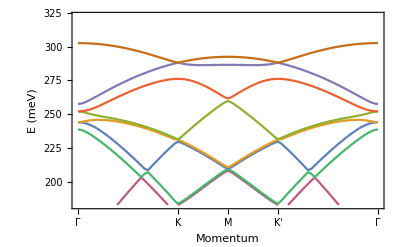

```mathematica
(* Highest energy at Γ *)
topϵ=evTsimple[[NHilbert,1,2]];
(* Energy range to plot *)
eRange={topϵ-120,topϵ+20};
(* Make dispersion plot *)
ListLinePlot[evTsimple[[NHilbert-50;;NHilbert]],PlotRange->eRange,
Frame->True,
FrameTicks->{Automatic,{{{0,"Γ"},{1/3,"Κ"},{1/2,"Μ"},{2/3,"Κ'"},{1,"Γ"}},None}},
FrameTicksStyle->Directive[FontFamily->"Latin Modern Roman",Black,12],
GridLines->{{0,1/3,1/2,2/3,1},None},
FrameLabel->{Style["Momentum",FontFamily->"Latin Modern Roman",Black,12],Style["E (meV)",FontFamily->"Latin Modern Roman",Black,12]}]
```

## ARPES spectrum

Once you’ve selected a Hamiltonian system in the first few sections of the code, we can calculate the ARPES matrix elements. Depending on whether you are at K or at Γ, you need to specify different paths.

The code below calculates a path from Γ-K-M-K’-Γ. First it calculates the wavefunctions, then the overlap with the ARPES matrix, then finally it makes a nice broadened densityplot of the ARPES spectrum.

To have an overlap with the experimental value,

```mathematica
(* Define a path *)
(* The following is the path from -M/2-Γ-M/2 Γ-point bands *)
(* arange=hrange/2/Norm[(2*G1M+G2M)];
kbegin=-arange*(2*G1M+G2M);
kend=arange*(2*G1M+G2M); *)
kbegin=-MbigBZ/2;
kend=MbigBZ/2;

(* How many points along the lines (in momentum direction) *)
NrSteps=400; 
(* Set energy range *)
{ϵMin,ϵMax}={-(μShift*vrange-(topϵ-w0)),-(μShift*vrange-(topϵ-w0))+vrange}; (* Good values for Subscript[tWeS, 2] *)
(* Set the pointsize *)
ps=0.02;
(* Choose the nbx bands closest to charge neutrality for speed up *)
nbx=NHilbert; (* NHilbert means full spectrum *)

(* Compute the corresponding ARPES response (matrix elements) *)
evT={};
PList={};
PList2={};
(* Choose which element of Hilberst space corresponds to the physical ARPES matrix elements *)
iBZ=Position[BZList,{0,0}][[1,1]];
xmin=(iBZ-1)*NrStatesPerBZ+1;
xmax=iBZ*NrStatesPerBZ;
(* Pointsize cutoff - remove the point if it is not interesting *)
psCutOff=0.0005;
Monitor[For[x=0.0,x≤1.0,x=x+N[1/NrSteps],
{qx,qy}=x*kend+(1-x)*kbegin;
(* Compute the eigenvalues *)
esys=Eigensystem[(Hamiltonian/.{kx->qx,ky->qy})];
evals=esys[[1]];
evecs=esys[[2]];
(* Save the evals *)
AppendTo[evT,Transpose[{Table[x,{i,1,NHilbert}],Sort[evals]}]];
(* Run over the evals to find the weight *)
For[in=NHilbert-nbx+1,in≤NHilbert,in++,
SpecPS=ps*Sum[Abs[evecs[[in,ibzx]]]^2,{ibzx,xmin,xmax}];
If[SpecPS>psCutOff&&(evals[[in]]>ϵMin)&&(evals[[in]]<ϵMax),
(* Save the weight *)
AppendTo[PList,{x,evals[[in]],SpecPS}];
(* Save the plotvisualization *)
AppendTo[PList2,{Blue,PointSize[SpecPS],Point[{x,evals[[in]]}]}];
];
];
];,x];
(* Transpose the band-structure *)
evT=Transpose[evT];
```

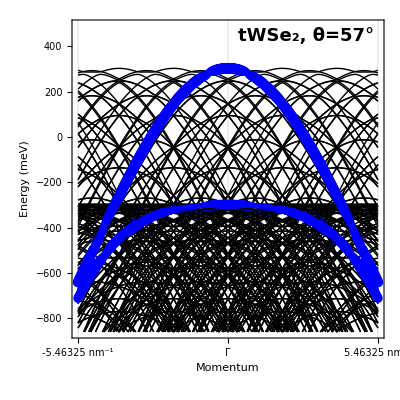

```mathematica
(* Finally create the plot *)
FigArpesPoint=Show[ListLinePlot[evT,PlotRange->{{0,1},{ϵMin,ϵMax}},AspectRatio->1,
PlotStyle->{{Black,Thin}},Frame->True,
FrameLabel->{Style["Momentum",FontFamily->"Latin Modern Roman",Black,FontSize->14],Style["Energy (meV)",FontFamily->"Latin Modern Roman",Black,FontSize->14]},
FrameTicksStyle->Directive[FontFamily->"Latin Modern Roman",Black,12],
FrameTicks->{{Automatic,None},{{{0,Style[ToString[-Norm[kend]]<>" nm^-1",12,FontFamily->"Latin Modern Roman"]},{0.5,Style["Γ",12,FontFamily->"Latin Modern Roman"]},{1,Style[ToString[Norm[kend]]<>" nm^-1",12,FontFamily->"Latin Modern Roman"]}},None}},
GridLines->{{0,0.5,1},None}],
Graphics[{PList2,
Text[Style["tWSe_2, θ=57°",Bold,FontFamily->"Latin Modern Roman",FontSize->18,Background->White],Scaled[{0.75,0.95}]]
}],
ImageSize->400]
```

```mathematica
(* Convert the 'dot' picture into a false color-plot *)
Clear[Ps,x,ϵ]
(* Set broadening of the bands *)
γE=50;
γK=0.004;
(* Set energy steps *)
ϵSteps=100;
(* Set momentum steps *)
kSteps=100;
(* Set Temperature (for states above Fermi level) *)
T=50;
(* Set Fermi level *)
μ=topϵ;
(* Define Lorentzian *)
Ps[x_,ϵ_]:=Total[PList[[;;,3]]/((x-PList[[;;,1]])^2+γK^2)/((ϵ-PList[[;;,2]])^2+γE^2)];
(* Convert to false color plot *)
Monitor[arpesColorData=Flatten[Table[{x,ϵ,Ps[x,ϵ]*1/(Exp[(ϵ-μ)/T]+1)},{x,0,1,N[1/kSteps]},{ϵ,ϵMin,ϵMax,(ϵMax-ϵMin)/ϵSteps}],1];,{x,ϵ}];
```

```mathematica
(* Make the visualization of the ARPES data *)
ImgARPESplot=Image[ListDensityPlot[arpesColorData,
PlotRange->{{0,1},{ϵMin,ϵMax},{0,0.5*Max[arpesColorData[[;;,3]]]}},
ColorFunction->(ColorData["GrayTones"][1-#] &),
ClippingStyle->Automatic,
AspectRatio->1.1,
Frame->False]];
(* Now put the frame around *)
FigARPES=ListDensityPlot[{{-10,-10,0},{-11,-11,0},{-10,-11,0}},
PlotRange->{{0,1},{ϵMin,ϵMax},{0,0.5*Max[arpesColorData[[;;,3]]]}},
ColorFunction->Opacity[1],
ClippingStyle->Automatic,
AspectRatio->1.1,
FrameLabel->{None,Style["Energy (meV)",FontFamily->"Latin Modern Roman",Black,FontSize->14]},
FrameTicksStyle->Directive[FontFamily->"Latin Modern Roman",Black,12],
PlotLabel->Style["tWSe_2, θ="<>ToString[60-θdeg]<>"°",Bold,FontFamily->"Latin Modern Roman",FontSize->16,Black,Background->White],
FrameTicks->{{Automatic,None},{{{0,Style["-Μ/2",12,FontFamily->"Latin Modern Roman"]},{0.5,Style["Γ",12,FontFamily->"Latin Modern Roman"]},{1,Style["Μ/2",12,FontFamily->"Latin Modern Roman"]}},None}},
GridLines->{{0,0.5,1},None},
Prolog->Inset[ImgARPESplot,{0.5,(ϵMin+ϵMax)/2},Automatic,1.04]]
```

-Graphics-